```mathematica
(* 

   Differential Operator  D = - 1/2 d^2/dtheta^2 +  g^2(1-  Cos[thets])
 
Flux Basis phi(m)  = Exp[i m theta] 

(m^2/2)phi_m  + (g^2/2)(2 phi_m -  (phi_m+1 + phi_m-1)) = lambda phi_m  l = -L, L +1 ,,,,-1,0,1,... L

WHAT ABOUT 1/2 INTEGER FLUX  m = +/-1/2   +/- 3/2 ...
*)

 Llist[g_,L_] := Table [ - 1/(2 g^2) ,2 L] 
 Ldown[g_,L_] := DiagonalMatrix[Llist[g,L],1]
Lup[g_,L_] := DiagonalMatrix[Llist[g,L],-1]
LzLz[g_,L_] := DiagonalMatrix[Table[g^2 m^2 /2  +  (1/g^2),{m,-L, L }] ]
```

```mathematica
FluxPlaqOperator[g_,L_]  := LzLz[g,L]+  Ldown[g,L]+  Lup[g,L]
```

```mathematica
MatrixForm[FluxPlaqOperator[1.,4]//N]
```

(9. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.5 | 5.5 | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 3. | -0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.5 | 1.5 | -0.5 | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.5 | 1. | -0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.5 | 1.5 | -0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 3. | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 5.5 | -0.5
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 9.)

```mathematica
MatrixPlot[%685]
```

MatrixPlot::mat0: Argument %685 at position 1 is not a matrix.

MatrixPlot[%685]

```mathematica
LupLdownCom[g_,L_] := Lup[g,L].Ldown[g,L]  - Ldown[g,L].Lup[g,L]
```

```mathematica
MatrixForm[LupLdownCom[g,4]]
```

(-1/(4 g^4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(4 g^4))

```mathematica
Sort[Eigenvalues[FluxPlaqOperator[0.1,4]//N]]
```

{4.91066,19.1336,41.2602,69.138,100.04,130.941,158.817,180.937,195.122}

```mathematica
EigValues = Sort[Eigenvalues[FluxPlaqOperator[0.1,128]//N]]
```

{0.499687,1.49844,2.49593,3.49217,4.48715,5.48087,6.47333,7.46452,8.45444,9.44309,10.4305,11.4166,12.4014,13.385,14.3672,15.3482,16.3279,17.3063,18.2834,19.2592,20.2337,21.2069,22.1788,23.1494,24.1187,25.0867,26.0533,27.0187,27.9827,28.9454,29.9068,30.8668,31.8255,32.7829,33.739,34.6937,35.647,36.599,37.5497,38.499,39.4469,40.3935,41.3388,42.2826,43.2251,44.1662,45.106,46.0444,46.9813,47.917,48.8512,49.784,50.7154,51.6455,52.5741,53.5013,54.4272,55.3516,56.2746,57.1961,58.1163,59.035,59.9523,60.8682,61.7826,62.6956,63.6071,64.5172,65.4259,66.3331,67.2388,68.1431,69.046,69.9474,70.8475,71.7462,72.6439,73.5407,74.4371,75.3338,76.2315,77.1314,78.035,78.9438,79.8594,80.7831,81.7164,82.6599,83.6145,84.5804,85.5576,86.546,87.5455,88.5555,89.5758,90.606,91.6456,92.6942,93.7514,94.8168,95.89,96.9708,98.0586,99.1533,100.254,101.362,102.475,103.593,104.717,105.846,106.98,108.118,109.261,110.407,111.557,112.71,113.867,115.027,116.189,117.354,118.521,119.69,120.861,122.034,123.208,124.383,125.559,126.735,127.913,129.09,130.267,131.445,132.621,133.798,134.973,136.147,137.32,138.492,139.662,140.83,141.996,143.16,144.321,145.479,146.634,147.787,148.935,150.081,151.222,152.36,153.493,154.622,155.746,156.865,157.979,159.088,160.191,161.289,162.38,163.466,164.545,165.617,166.683,167.741,168.792,169.836,170.872,171.9,172.919,173.931,174.933,175.926,176.91,177.885,178.85,179.805,180.749,181.683,182.606,183.517,184.417,185.306,186.181,187.045,187.895,188.731,189.554,190.362,191.155,191.933,192.695,193.439,194.166,194.874,195.562,196.229,196.873,197.493,198.084,198.646,199.153,199.678,199.947,200.662,200.698,201.741,201.742,202.952,202.952,204.281,204.281,205.714,205.714,207.245,207.245,208.871,208.871,210.59,210.59,212.402,212.402,214.31,214.31,216.314,216.314,218.419,218.419,220.63,220.63,222.952,222.952,225.392,225.392,227.959,227.959,230.665,230.665,233.522,233.522,236.548,236.548,239.765,239.765,243.2,243.2,246.894,246.894,250.902,250.902,255.306,255.306,260.244,260.244,265.981,265.981,273.2,273.2}

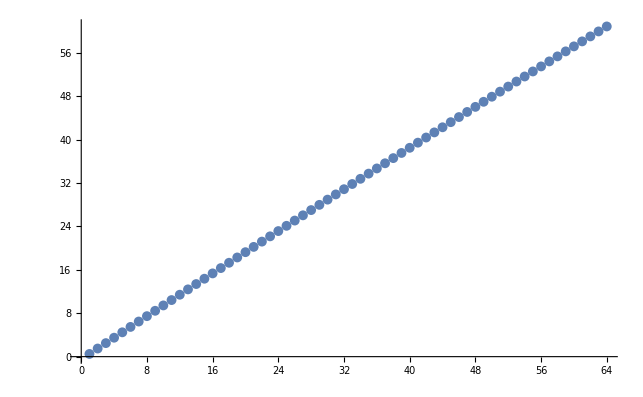

```mathematica
ListPlot[EigValues[[1;;64]]]
```

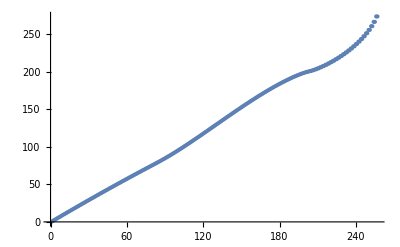

```mathematica
ListPlot[EigValues]
```

```mathematica
EigenPlot := ListPlot[EigValues]
```

```mathematica
f[x_]= Fit[EigValues, {1,x, x ^2,x^3,x^4}, x]
```

5.49982+0.48879 x+0.00825197 x^2-0.0000469036 x^3+8.7197×10^-8 x^4

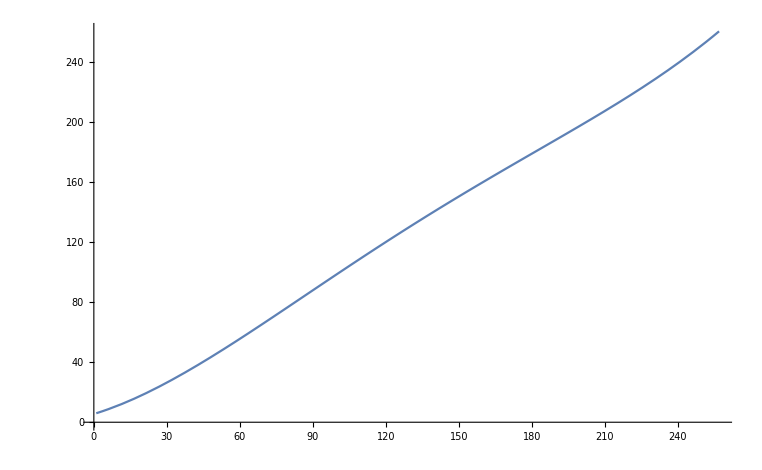

```mathematica
Plot[Evaluate[f[x]],{x,1,257}]
```

```mathematica
EigenValue100 = Sort[Eigenvalues[FluxPlaqOperator[0.01,128]/10000//N]]
```

{0.0000847441,0.000319795,0.00069306,0.0012127,0.00187995,0.00269503,0.0036579,0.00476847,0.00602657,0.00743205,0.00898469,0.0106843,0.0125305,0.0145232,0.016662,0.0189466,0.0213766,0.0239518,0.0266717,0.0295359,0.032544,0.0356956,0.0389901,0.0424271,0.0460061,0.0497266,0.0535879,0.0575896,0.0617311,0.0660116,0.0704306,0.0749875,0.0796815,0.084512,0.0894783,0.0945795,0.099815,0.105184,0.110686,0.116319,0.122084,0.127978,0.134002,0.140155,0.146435,0.152841,0.159373,0.16603,0.17281,0.179713,0.186738,0.193883,0.201148,0.208531,0.216032,0.223649,0.231381,0.239226,0.247185,0.255256,0.263436,0.271726,0.280124,0.288629,0.297239,0.305954,0.314771,0.32369,0.332709,0.341827,0.351043,0.360355,0.369761,0.379262,0.388854,0.398537,0.408309,0.418169,0.428115,0.438146,0.44826,0.458456,0.468732,0.479087,0.48952,0.500028,0.51061,0.521265,0.53199,0.542785,0.553648,0.564577,0.575571,0.586628,0.597745,0.608923,0.620159,0.63145,0.642797,0.654196,0.665647,0.677147,0.688696,0.70029,0.711929,0.72361,0.735333,0.747094,0.758894,0.770729,0.782598,0.794499,0.80643,0.818391,0.830378,0.842391,0.854427,0.866484,0.878561,0.890657,0.902768,0.914894,0.927032,0.939182,0.95134,0.963506,0.975677,0.987851,1.00003,1.0122,1.02438,1.03655,1.04872,1.06087,1.07302,1.08516,1.09729,1.1094,1.12149,1.13357,1.14563,1.15766,1.16968,1.18166,1.19362,1.20556,1.21746,1.22933,1.24116,1.25296,1.26472,1.27645,1.28813,1.29977,1.31136,1.32291,1.33441,1.34586,1.35726,1.36861,1.3799,1.39113,1.40231,1.41343,1.42448,1.43548,1.44641,1.45727,1.46807,1.47879,1.48945,1.50003,1.51054,1.52097,1.53132,1.5416,1.5518,1.56191,1.57194,1.58189,1.59175,1.60152,1.6112,1.62079,1.63029,1.6397,1.64901,1.65823,1.66735,1.67637,1.68528,1.6941,1.70282,1.71143,1.71993,1.72833,1.73662,1.7448,1.75287,1.76083,1.76867,1.77641,1.78402,1.79152,1.79891,1.80617,1.81332,1.82034,1.82725,1.83403,1.84068,1.84721,1.85362,1.8599,1.86605,1.87208,1.87797,1.88374,1.88937,1.89487,1.90024,1.90548,1.91058,1.91554,1.92037,1.92507,1.92962,1.93404,1.93832,1.94247,1.94647,1.95033,1.95405,1.95763,1.96107,1.96436,1.96751,1.97052,1.97338,1.9761,1.97868,1.98111,1.98339,1.98553,1.98752,1.98937,1.99107,1.99262,1.99403,1.99529,1.9964,1.99736,1.99817,1.99884,1.99936,1.99973,1.99994}

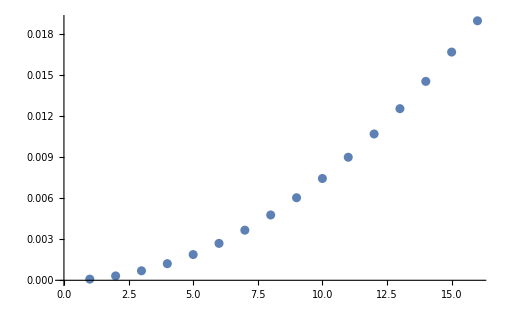

```mathematica
ListPlot[EigenValue100[[1;;16]]]
```

```mathematica
(*   H =  (1/2) (d/d theta)^2 + g^2 Cos[theta]  ==>  A  - d^2/dtheat^2 + g^2 Cos[theta}
 
2 L + 1 lattice a = 2 Pi/( 2 L +1)   theta_n = n a  

(phi_n - (1/2) phi_n-1 - (1/2) pbi_n+1)/a^2 + g^2(1 -  Cos[ a n]) phi_n = lamba phi_n 

WHAT ABOUT 1/2 INTEGER FLUX  ==> Antiperiodic B.C.
*)
```

```mathematica
a[L_] := 2 Pi/(2 L + 1);
```

```mathematica
CosList[g_,L_]:= Table[g^2/a[L]^2  + (1/g^2) (1- Cos[a[L] n]),{n,2 L +1}]
```

```mathematica
CosList[g,4]
```

{(81 g^2)/(4 π^2)+(1-Cos[(2 π)/9])/g^2,(81 g^2)/(4 π^2)+(1-Sin[π/18])/g^2,3/(2 g^2)+(81 g^2)/(4 π^2),(81 g^2)/(4 π^2)+(1+Cos[π/9])/g^2,(81 g^2)/(4 π^2)+(1+Cos[π/9])/g^2,3/(2 g^2)+(81 g^2)/(4 π^2),(81 g^2)/(4 π^2)+(1-Sin[π/18])/g^2,(81 g^2)/(4 π^2)+(1-Cos[(2 π)/9])/g^2,(81 g^2)/(4 π^2)}

```mathematica
Hop[L_,g_]:= Table[-g^2/(2 a[L]^2), 2L]
```

```mathematica
PlaqOperator[g_,L_] :=  DiagonalMatrix[CosList[g,L]] +  DiagonalMatrix[Hop[L,g],1] +DiagonalMatrix[Hop[L,g],-1] + DiagonalMatrix[{-1/(2 a[L]^2)},2 L] + DiagonalMatrix[{-1/(2 a[L]^2)},-2 L]
```

```mathematica
Clear[Amatrix]
```

```mathematica
Amatrix = PlaqOperator[g_,4]
```

{{(1-Cos[(2 π)/9])/g_^2+(81 g_^2)/(4 π^2),-(81 g_^2)/(8 π^2),0,0,0,0,0,0,-81/(8 π^2)},{-(81 g_^2)/(8 π^2),(81 g_^2)/(4 π^2)+(1-Sin[π/18])/g_^2,-(81 g_^2)/(8 π^2),0,0,0,0,0,0},{0,-(81 g_^2)/(8 π^2),3/(2 g_^2)+(81 g_^2)/(4 π^2),-(81 g_^2)/(8 π^2),0,0,0,0,0},{0,0,-(81 g_^2)/(8 π^2),(1+Cos[π/9])/g_^2+(81 g_^2)/(4 π^2),-(81 g_^2)/(8 π^2),0,0,0,0},{0,0,0,-(81 g_^2)/(8 π^2),(1+Cos[π/9])/g_^2+(81 g_^2)/(4 π^2),-(81 g_^2)/(8 π^2),0,0,0},{0,0,0,0,-(81 g_^2)/(8 π^2),3/(2 g_^2)+(81 g_^2)/(4 π^2),-(81 g_^2)/(8 π^2),0,0},{0,0,0,0,0,-(81 g_^2)/(8 π^2),(81 g_^2)/(4 π^2)+(1-Sin[π/18])/g_^2,-(81 g_^2)/(8 π^2),0},{0,0,0,0,0,0,-(81 g_^2)/(8 π^2),(1-Cos[(2 π)/9])/g_^2+(81 g_^2)/(4 π^2),-(81 g_^2)/(8 π^2)},{-81/(8 π^2),0,0,0,0,0,0,-(81 g_^2)/(8 π^2),(81 g_^2)/(4 π^2)}}

```mathematica
MatrixForm[Amatrix]
```

((1-Cos[(2 π)/9])/g_^2+(81 g_^2)/(4 π^2) | -(81 g_^2)/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | -81/(8 π^2)
-(81 g_^2)/(8 π^2) | (81 g_^2)/(4 π^2)+(1-Sin[π/18])/g_^2 | -(81 g_^2)/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0
0 | -(81 g_^2)/(8 π^2) | 3/(2 g_^2)+(81 g_^2)/(4 π^2) | -(81 g_^2)/(8 π^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | -(81 g_^2)/(8 π^2) | (1+Cos[π/9])/g_^2+(81 g_^2)/(4 π^2) | -(81 g_^2)/(8 π^2) | 0 | 0 | 0 | 0
0 | 0 | 0 | -(81 g_^2)/(8 π^2) | (1+Cos[π/9])/g_^2+(81 g_^2)/(4 π^2) | -(81 g_^2)/(8 π^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | -(81 g_^2)/(8 π^2) | 3/(2 g_^2)+(81 g_^2)/(4 π^2) | -(81 g_^2)/(8 π^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | -(81 g_^2)/(8 π^2) | (81 g_^2)/(4 π^2)+(1-Sin[π/18])/g_^2 | -(81 g_^2)/(8 π^2) | 0
0 | 0 | 0 | 0 | 0 | 0 | -(81 g_^2)/(8 π^2) | (1-Cos[(2 π)/9])/g_^2+(81 g_^2)/(4 π^2) | -(81 g_^2)/(8 π^2)
-81/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | -(81 g_^2)/(8 π^2) | (81 g_^2)/(4 π^2))

```mathematica
MatrixForm[PlaqOperator[0.1,4]//N]
```

(23.4161 | -0.0102588 | 0. | 0. | 0. | 0. | 0. | 0. | -1.02588
-0.0102588 | 82.6557 | -0.0102588 | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0102588 | 150.021 | -0.0102588 | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0102588 | 193.99 | -0.0102588 | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0102588 | 193.99 | -0.0102588 | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0102588 | 150.021 | -0.0102588 | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.0102588 | 82.6557 | -0.0102588 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0102588 | 23.4161 | -0.0102588
-1.02588 | 0. | 0. | 0. | 0. | 0. | 0. | -0.0102588 | 0.0205175)

```mathematica
EigenValueTheta = Sort[Eigenvalues[PlaqOperator[0.1,256]]]
```

{-3266.74,1.4961,1.63964,3.4805,3.69187,5.45246,5.71379,7.412,7.71426,9.35917,9.69664,11.294,11.6626,13.2165,13.6132,15.1267,15.549,17.0246,17.4705,18.9104,19.3781,20.7839,21.2721,22.6452,23.1526,24.4944,25.0198,26.3315,26.8738,28.1565,28.7149,29.9695,30.5431,31.7704,32.3584,33.5593,34.1611,35.3362,35.9511,37.1011,37.7285,38.8541,39.4934,40.5952,41.2459,42.3243,42.986,44.0416,44.7137,45.7471,46.4291,47.4407,48.1323,49.1225,49.8232,50.7925,51.502,52.4507,53.1686,54.0972,54.8231,55.7319,56.4655,57.3549,58.0959,58.9661,59.7142,60.5657,61.3205,62.1535,62.9148,63.7297,64.4972,65.2942,66.0676,66.847,67.6261,68.3881,69.1727,69.9176,70.7074,71.4355,72.2301,72.9417,73.741,74.4362,75.24,75.9191,76.7272,77.3904,78.2024,78.8499,79.6658,80.2979,81.1173,81.7341,82.557,83.1586,83.9847,84.5715,85.4005,85.9726,86.8045,87.362,88.1965,88.7397,89.5765,90.1055,90.9446,91.4596,92.3007,92.8018,93.6448,94.1321,94.9768,95.4506,96.2967,96.757,97.6045,98.0515,98.9,99.3338,100.183,100.604,101.454,101.862,102.713,103.108,103.959,104.341,105.193,105.563,106.414,106.771,107.622,107.967,108.818,109.15,110.,110.32,111.169,111.478,112.326,112.622,113.468,113.752,114.597,114.869,115.713,115.973,116.814,117.062,117.901,118.137,118.973,119.198,120.03,120.243,121.072,121.273,122.099,122.287,123.109,123.285,124.101,124.266,125.077,125.23,126.034,126.174,126.971,127.099,127.888,128.004,128.782,128.885,129.652,129.742,130.495,130.57,131.306,131.366,132.081,132.124,132.814,132.84,133.519,133.529,134.227,134.229,134.967,134.968,135.744,135.745,136.554,136.554,137.389,137.389,138.247,138.247,139.126,139.126,140.021,140.021,140.933,140.933,141.859,141.859,142.799,142.799,143.75,143.75,144.712,144.712,145.685,145.685,146.667,146.667,147.659,147.659,148.658,148.658,149.664,149.664,150.678,150.678,151.698,151.698,152.724,152.724,153.756,153.756,154.792,154.792,155.833,155.833,156.878,156.878,157.926,157.926,158.978,158.978,160.032,160.032,161.089,161.089,162.148,162.148,163.208,163.208,164.27,164.27,165.333,165.333,166.396,166.396,167.459,167.459,168.522,168.522,169.584,169.584,170.645,170.645,171.705,171.705,172.763,172.763,173.818,173.818,174.871,174.871,175.922,175.922,176.968,176.968,178.011,178.011,179.05,179.05,180.084,180.084,181.112,181.112,182.136,182.136,183.152,183.152,184.163,184.163,185.166,185.166,186.161,186.161,187.148,187.148,188.125,188.125,189.093,189.093,190.05,190.05,190.996,190.996,191.928,191.928,192.848,192.848,193.752,193.752,194.639,194.639,195.507,195.507,196.355,196.355,197.178,197.178,197.971,197.971,198.725,198.73,199.413,199.448,199.975,200.138,200.525,200.836,201.204,201.573,201.957,202.35,202.753,203.163,203.581,204.006,204.438,204.876,205.319,205.769,206.224,206.684,207.149,207.619,208.093,208.573,209.057,209.545,210.038,210.534,211.036,211.541,212.05,212.563,213.08,213.601,214.125,214.654,215.186,215.722,216.261,216.804,217.35,217.9,218.454,219.01,219.571,220.134,220.701,221.272,221.845,222.422,223.003,223.586,224.173,224.763,225.356,225.952,226.552,227.155,227.76,228.369,228.981,229.597,230.215,230.836,231.461,232.088,232.719,233.352,233.989,234.629,235.272,235.917,236.566,237.218,237.872,238.53,239.191,239.855,240.521,241.191,241.863,242.539,243.217,243.899,244.583,245.271,245.961,246.654,247.35,248.049,248.751,249.456,250.164,250.875,251.589,252.306,253.025,253.748,254.473,255.201,255.933,256.667,257.404,258.144,258.887,259.633,260.381,261.133,261.887,262.645,263.405,264.169,264.935,265.704,266.476,267.251,268.029,268.81,269.593,270.38,271.169,271.962,272.757,273.556,274.357,275.161,275.968,276.778,277.591,278.407,279.226,280.048,280.872,281.7,282.53,283.364,284.2,285.04,285.882,286.728,287.576,288.427,289.281,290.139,290.999,291.862,292.728,293.597,294.469,295.344,296.222,297.103,297.987,298.874,299.764,300.657,301.553,302.452,303.354,304.258,305.166,306.077,306.991,307.908,308.829,309.752,310.678,311.607,312.539,313.474,314.413,315.354,316.298,317.246,318.196,319.15,320.106,321.066,322.029,322.995,323.964,324.936,325.911,326.889,327.871,328.855,329.842,330.833,331.827,332.824,3400.07}

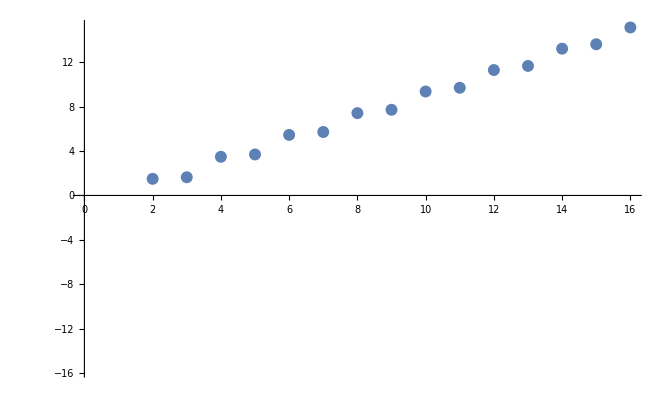

```mathematica
ListPlot[EigenValueTheta[[1;;16]]]
```

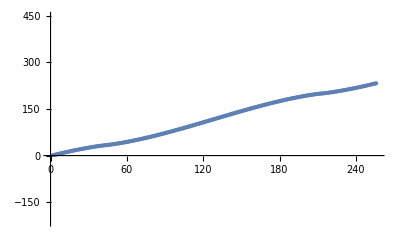

```mathematica
EigenPlotTheta = ListPlot[EigenValueTheta]
```

```mathematica
PlaqPeriodic = Sort[Eigenvalues[PlaqOperator[0.01,128]]]
```

{-834.86,3.15494,12.1187,12.1195,27.0525,27.0525,47.9464,47.9464,74.7886,74.7886,107.563,107.563,146.25,146.25,190.827,190.827,241.266,241.266,297.539,297.539,359.61,359.61,427.444,427.444,500.998,500.998,580.231,580.231,665.093,665.093,755.535,755.535,838.183,851.503,851.503,952.938,952.938,1059.78,1059.78,1171.97,1171.97,1289.43,1289.43,1412.1,1412.1,1539.9,1539.9,1672.76,1672.76,1810.59,1810.59,1953.33,1953.33,2100.87,2100.87,2253.13,2253.13,2410.02,2410.02,2571.45,2571.45,2737.31,2737.31,2907.52,2907.52,3081.97,3081.97,3260.55,3260.55,3443.17,3443.17,3629.7,3629.7,3820.03,3820.03,4014.06,4014.06,4211.67,4211.67,4412.74,4412.74,4617.15,4617.15,4824.78,4824.78,5035.5,5035.5,5249.18,5249.18,5465.71,5465.71,5684.95,5684.95,5906.76,5906.76,6131.02,6131.02,6357.6,6357.6,6586.35,6586.35,6817.14,6817.14,7049.83,7049.83,7284.29,7284.29,7520.37,7520.37,7757.94,7757.94,7996.84,7996.84,8236.94,8236.94,8478.09,8478.09,8720.16,8720.16,8962.99,8962.99,9206.44,9206.44,9450.36,9450.36,9694.61,9694.61,9939.05,9939.05,10183.5,10183.5,10427.9,10427.9,10672.,10672.,10915.7,10915.7,11158.8,11158.8,11401.3,11401.3,11642.9,11642.9,11883.6,11883.6,12123.1,12123.1,12361.4,12361.4,12598.2,12598.2,12833.5,12833.5,13067.1,13067.1,13298.8,13298.8,13528.6,13528.6,13756.3,13756.3,13981.7,13981.7,14204.8,14204.8,14425.3,14425.3,14643.2,14643.2,14858.4,14858.4,15070.6,15070.6,15279.8,15279.8,15485.8,15485.8,15688.6,15688.6,15887.9,15887.9,16083.7,16083.7,16275.9,16275.9,16464.4,16464.4,16649.,16649.,16829.6,16829.6,17006.1,17006.1,17178.5,17178.5,17346.5,17346.5,17510.2,17510.2,17669.3,17669.3,17823.9,17823.9,17973.8,17973.8,18119.,18119.,18259.3,18259.3,18394.6,18394.6,18525.,18525.,18650.2,18650.2,18770.3,18770.3,18885.1,18885.1,18994.6,18994.6,19098.8,19098.8,19197.5,19197.5,19290.7,19290.7,19378.4,19378.4,19460.4,19460.4,19536.8,19536.8,19607.5,19607.5,19672.5,19672.5,19731.7,19731.7,19785.,19785.,19832.5,19832.5,19874.2,19874.2,19909.9,19909.9,19939.7,19939.7,19963.6,19963.6,19981.5,19981.5,19993.4,19993.4,19999.3,19999.5}

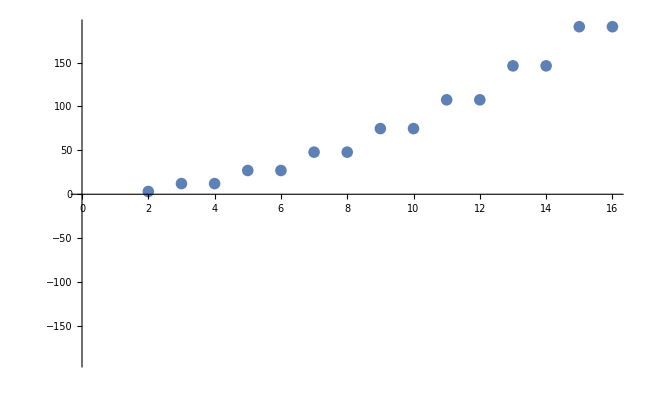

```mathematica
ListPlot[Take[PlaqPeriodic,16]]
```

```mathematica
Gauge = Sort[Flatten[Table[n12*n12 + n23*n23,{n12,-4,4},{n23,-4,4}]]]
```

{0,1,1,1,1,2,2,2,2,4,4,4,4,5,5,5,5,5,5,5,5,8,8,8,8,9,9,9,9,10,10,10,10,10,10,10,10,13,13,13,13,13,13,13,13,16,16,16,16,17,17,17,17,17,17,17,17,18,18,18,18,20,20,20,20,20,20,20,20,25,25,25,25,25,25,25,25,32,32,32,32}

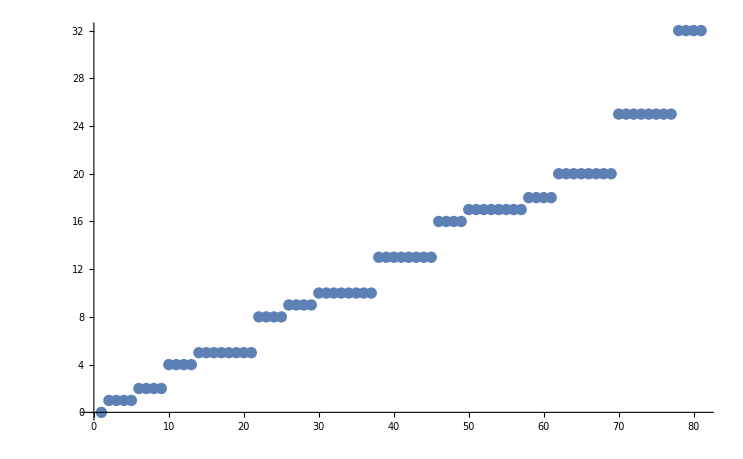

```mathematica
ListPlot[Gauge]
```

```mathematica
EigValues-  EigenValueTheta
```

{820.358,0.00936814,0.709966,0.0469976,0.613144,0.115109,0.583964,0.21411,0.604825,0.344474,0.669491,0.506743,0.775159,0.701543,0.920517,0.929599,1.10507,1.19175,1.32886,1.48898,1.59232,1.82245,1.89627,2.19353,2.24189,2.60384,2.63075,3.0554,3.06493,3.55067,3.54717,4.09276,4.0811,4.68575,4.67166,5.33517,5.32598,6.04906,6.05475,6.83989,6.87207,7.72376,7.77303,8.68392,8.68063,9.61667,9.50347,10.4415,10.2231,11.1587,10.8512,11.7841,11.3981,12.3282,11.871,12.7982,12.275,13.1994,12.6142,13.5357,12.8917,13.8105,13.1105,14.0264,13.273,14.186,13.3812,14.2913,13.4373,14.3445,13.443,14.3472,13.4001,14.3015,13.3105,14.2093,13.1765,14.0733,13.0014,13.898,12.7912,13.6911,12.5554,13.4642,12.3072,13.231,12.0599,13.0034,11.8235,12.7893,11.6032,12.5917,11.4005,12.4106,11.2145,12.2446,11.0434,12.092,10.8856,11.951,10.7393,11.82,10.6029,11.6976,10.4754,11.5827,10.3555,11.4742,10.2425,11.3714,10.1355,11.2736,10.0339,11.1802,9.93719,11.0907,9.84484,11.0045,9.75643,10.9213,9.67158,10.8408,9.58996,10.7625,9.51127,10.6863,9.43521,10.6119,9.36154,10.5389,9.29002,10.4672,9.22042,10.3966,9.15253,10.3269,9.08615,10.2578,9.02107,10.1891,8.95711,10.1207,8.89407,10.0524,8.83174,9.98396,8.76995,9.9152,8.70847,9.8459,8.64712,9.77587,8.58566,9.70488,8.52387,9.6327,8.46151,9.55908,8.39831,9.48374,8.334,9.40641,8.26827,9.32675,8.20078,9.24443,8.13118,9.15905,8.05905,9.07018,7.98395,8.97734,7.90535,8.87998,7.82268,8.77747,7.73527,8.66908,7.64235,8.55396,7.54302,8.43113,7.43621,8.29937,7.32062,8.15723,7.19468,8.0029,7.0564,7.83408,6.9032,7.64773,6.73166,7.43971,6.53692,7.20399,6.31166,6.93109,6.04303,6.60547,5.69421,6.21871,5.13627,5.85091,4.60629,5.64908,4.45051,5.66035,4.55617,5.88249,4.92379,6.31709,5.65112,6.92412,6.43066,7.58757,7.06811,8.24497,7.67905,8.90512,8.3,9.5847,8.94589,10.2962,9.62727,11.0496,10.3532,11.8544,11.1324,12.7199,11.9738,13.6562,12.887,14.6742,13.883,15.7867,14.9743,17.0088,16.1758,18.3588,17.5059,19.8597,18.9872,21.541,20.6495,23.4425,22.5322,25.62,24.6913,28.1574,27.2106,31.1929,30.2282,34.9915,34.009,40.2372,-580.149}

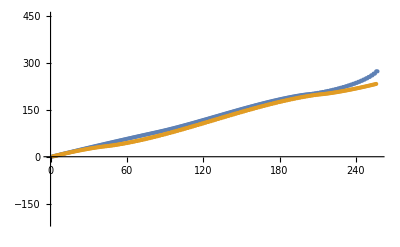

-60.6804+2.85279 x-0.0202962 x^2+0.0000818085 x^3-1.03306×10^-7 x^4

```mathematica
ListPlot[{EigValues, EigenValueTheta}]

fTheta[x_]= Fit[EigenValueTheta, {1,x, x ^2,x^3,x^4}, x]
```

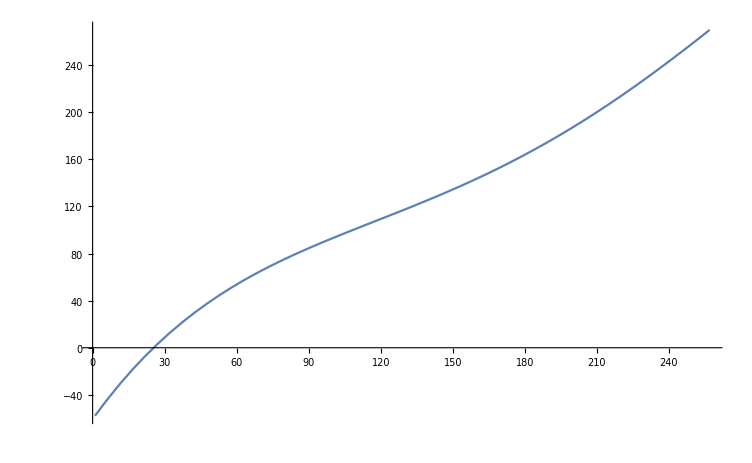

```mathematica
Plot[fTheta[x],{x,1,257}]
```

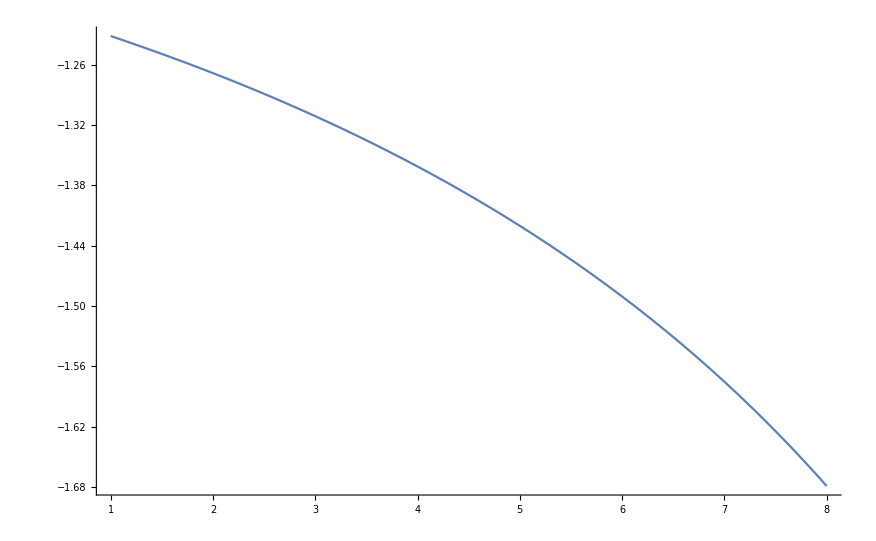

```mathematica
Plot[ (f[x]-fTheta[x])/(f[x] + fTheta[x]) ,{x,1,8}]
```

```mathematica
DiffEigValues := EigValues- EigenValueTheta
```

```mathematica
SumEigValues := EigValues+ EigenValueTheta
```

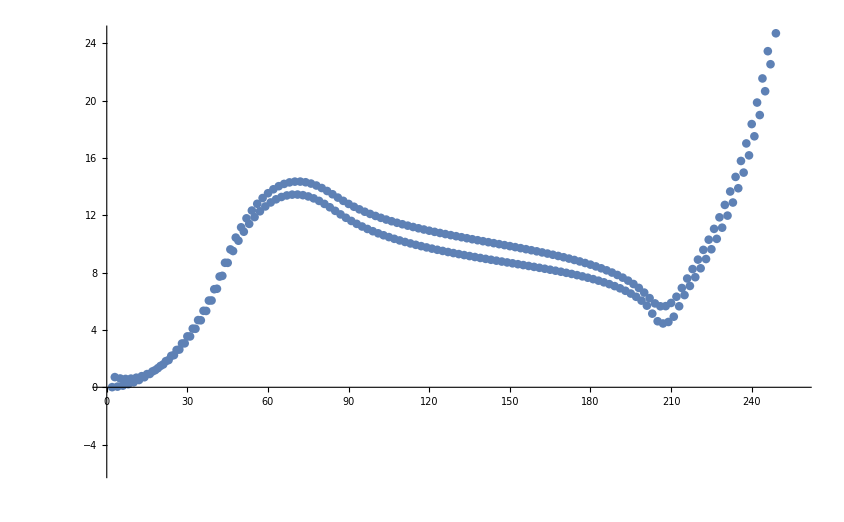

```mathematica
ListPlot[DiffEigValues]
```

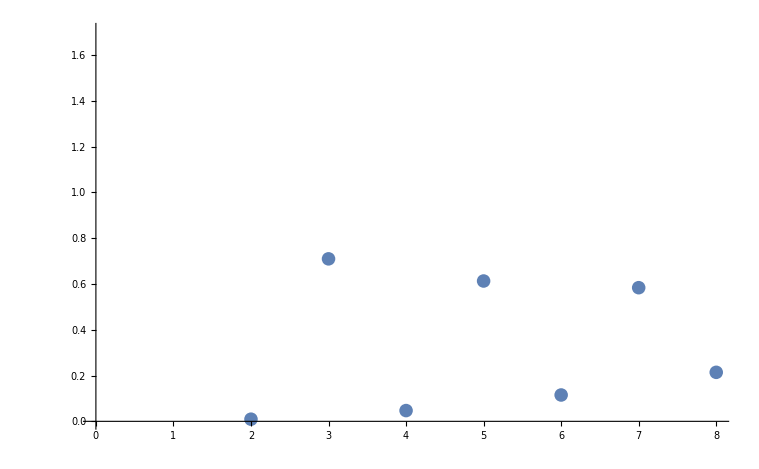

```mathematica
ListPlot[DiffEigValues[[1;;8]]]
```

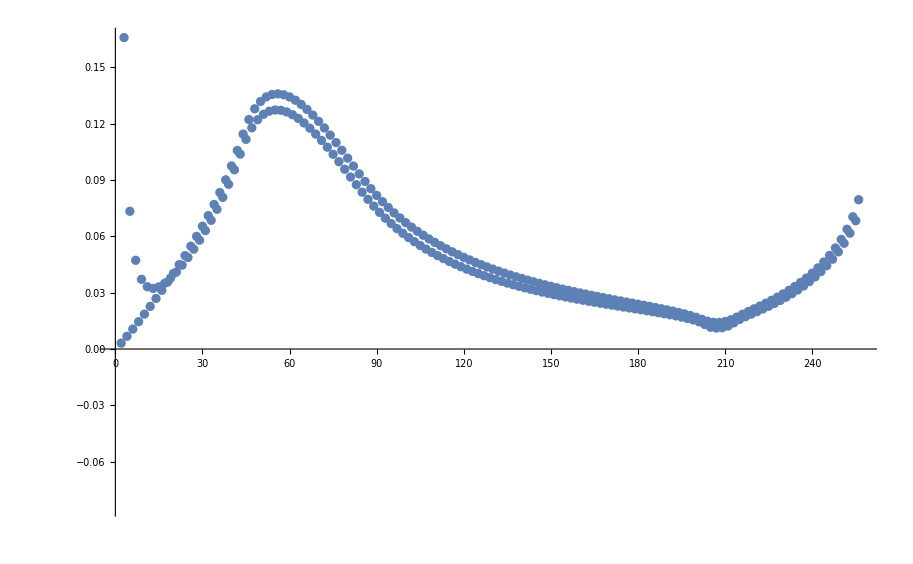

```mathematica
ListPlot[DiffEigValues/SumEigValues]
```

```mathematica
EigenValueTheta100 = Sort[Eigenvalues[PlaqOperator[100,128]/10000//N]]
```

{0.124031,0.496108,1.11617,1.98414,3.09986,4.4632,6.07392,7.93184,10.0366,12.388,14.9855,17.829,20.9178,24.2517,27.8299,31.6522,35.7176,40.0261,44.5764,49.3685,54.401,59.6739,65.1855,70.936,76.9236,83.1484,89.6083,96.3036,103.232,110.394,117.787,125.411,133.264,141.346,149.654,158.189,166.948,175.931,185.135,194.56,204.204,214.067,224.145,234.439,244.944,255.663,266.591,277.729,289.072,300.622,312.373,324.329,336.482,348.835,361.383,374.127,387.062,400.19,413.504,427.007,440.693,454.563,468.612,482.842,497.246,511.827,526.577,541.5,556.588,571.845,587.262,602.842,618.579,634.475,650.521,666.723,683.07,699.568,716.206,732.99,749.91,766.97,784.161,801.487,818.939,836.521,854.224,872.052,889.994,908.057,926.229,944.516,962.906,981.407,1000.01,1018.71,1037.5,1056.4,1075.38,1094.45,1113.61,1132.85,1152.17,1171.57,1191.04,1210.58,1230.19,1249.87,1269.61,1289.42,1309.27,1329.18,1349.14,1369.16,1389.21,1409.31,1429.44,1449.62,1469.82,1490.06,1510.32,1530.61,1550.92,1571.24,1591.58,1611.94,1632.3,1652.67,1673.04,1693.41,1713.78,1734.14,1754.5,1774.84,1795.16,1815.47,1835.76,1856.02,1876.26,1896.47,1916.64,1936.78,1956.87,1976.93,1996.94,2016.9,2036.81,2056.67,2076.47,2096.21,2115.89,2135.5,2155.04,2174.52,2193.91,2213.23,2232.47,2251.63,2270.7,2289.69,2308.58,2327.38,2346.07,2364.68,2383.17,2401.57,2419.85,2438.03,2456.09,2474.03,2491.86,2509.56,2527.14,2544.6,2561.92,2579.11,2596.17,2613.09,2629.87,2646.52,2663.01,2679.36,2695.56,2711.61,2727.5,2743.24,2758.82,2774.24,2789.49,2804.58,2819.5,2834.26,2848.83,2863.24,2877.47,2891.52,2905.39,2919.08,2932.58,2945.89,2959.02,2971.96,2984.7,2997.25,3009.6,3021.75,3033.71,3045.46,3057.01,3068.35,3079.49,3090.42,3101.14,3111.64,3121.94,3132.02,3141.88,3151.52,3160.95,3170.15,3179.13,3187.89,3196.43,3204.74,3212.82,3220.67,3228.29,3235.69,3242.85,3249.78,3256.47,3262.93,3269.16,3275.15,3280.9,3286.41,3291.68,3296.71,3301.5,3306.06,3310.36,3314.43,3318.25,3321.83,3325.16,3328.25,3331.1,3333.69,3336.04,3338.15,3340.01,3341.62,3342.98,3344.1,3344.97,3345.59,3345.96}

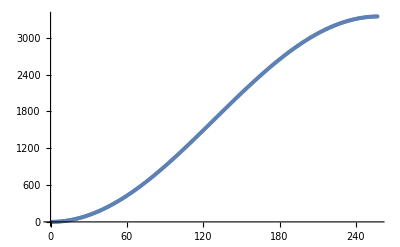

```mathematica
ListPlot[EigenValueTheta100 ]
```

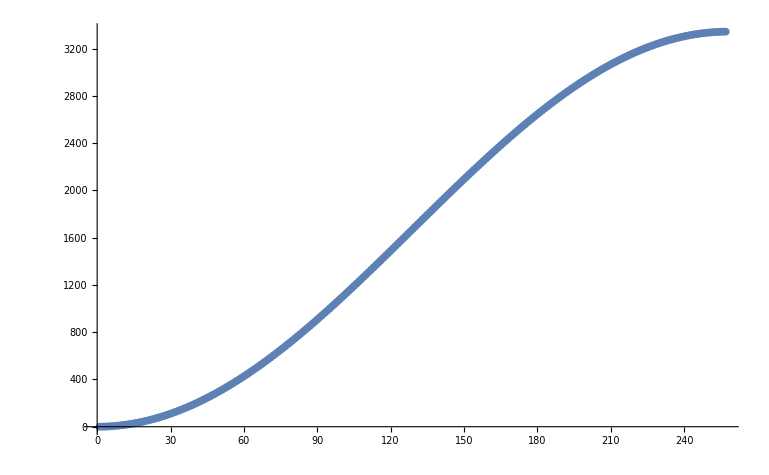

```mathematica
ListPlot[EigenValueTheta100 -EigenValue100]
```